## Blatt 9 WS 17/18

17.12.2017

Wir wollen die Matrixmethode auf einen "bunch-compressor" loslassen. Ein solcher compressor ist eine 4-Dipol Schikane, in unserem Fall benutzen wir die Parameter des BC2 von FLASH.

-Graphics-

Zur Illustration und definition einiger Paramter ein Bild.

Damit wir nicht schon beim Abschreiben der 6x6 Matrizen Fehler einbauen und wir überhaupt nicht so viel programmieren müssen benutzen wir ein "tool" das wir (die Studenten und ich) im Laufe vielen Übungen zur Beschleunigerphysik zusammen gebastelt haben. Das ersetzt keineswegs ein professionelles "tracking tool" wie ELEGANT oder MAD oder wie sie alle heissen, ist aber in Mathematica geschrieben und damit kennen wir uns ja aus.

Erst laden wir das package mal, das geht mit "Get[  " oder abgekürzt "<<".

```mathematica
AppendTo[$Path, "D:\\Benutzer\\jonas\\Studium\\Beschleunigerphysik\\beschleunigeruebungen"]; (* Muss wohl für jede Maschine angepasst werden *)
```

```mathematica
<<MyMachine`
```

Version 17.12.2017

Global`PlotLabel::shdw: Symbol PlotLabel appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`PlotStyle::shdw: Symbol PlotStyle appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Dann können wir mal schauen, was in diesem Packet so alles definiert ist. Das meiste davon werden wir jetzt nicht benötigen.

```mathematica
?MyMachine`*
```

kanteGen[dummy,ρ,ψ]: produces the 6x6 matrix of the edge of a magnet with bending radius ρ and deflection angle ψ

Wenn man auf die Namen klickt, bekommt man auch ein wenig Auskunft..

Natürlich kenn man jetzt alle 6x6 Matrizen.

```mathematica
drift[L]//MatrixForm
```

(1 | L | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | L | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
kante[0,ρ,ψ1]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
Tan[ψ1]/ρ | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | -Tan[ψ1]/ρ | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
dipol[L,ρ] //MatrixForm
```

(Cos[L/ρ] | ρ Sin[L/ρ] | 0 | 0 | 0 | ρ (1-Cos[L/ρ])
-Sin[L/ρ]/ρ | Cos[L/ρ] | 0 | 0 | 0 | Sin[L/ρ]
0 | 0 | 1 | L | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
-Sin[L/ρ] | -ρ (1-Cos[L/ρ]) | 0 | 0 | 1 | -ρ (L/ρ-Sin[L/ρ])
0 | 0 | 0 | 0 | 0 | 1)

So könnte man jetzt auch den ganzen Compressor hintereinander multiplizieren, Beispiel

```mathematica
dipol[L,ρ].kante[0.,ρ,ψ1]//MatrixForm
```

(Cos[L/ρ]+Sin[L/ρ] Tan[ψ1] | ρ Sin[L/ρ] | 0 | 0 | 0 | ρ (1-Cos[L/ρ])
-Sin[L/ρ]/ρ+(Cos[L/ρ] Tan[ψ1])/ρ | Cos[L/ρ] | 0 | 0 | 0 | Sin[L/ρ]
0 | 0 | 1-(L Tan[ψ1])/ρ | L | 0 | 0
0 | 0 | -Tan[ψ1]/ρ | 1 | 0 | 0
-Sin[L/ρ]-(1-Cos[L/ρ]) Tan[ψ1] | -ρ (1-Cos[L/ρ]) | 0 | 0 | 1 | -ρ (L/ρ-Sin[L/ρ])
0 | 0 | 0 | 0 | 0 | 1)

Das wollen wir aber ganz nicht tun sondern wir wollen die Fähigkeiten des "tools" ausnutzen und diesem die Arbeit überlassen.

Definieren wir erstmal die Parameter von BC2 :

```mathematica
parameter =  {θ->18. Degree,Larc->θ ρ, Leff->0.5,ρ->Leff/Sin[θ],Ld->Leff/Cos[θ],L2->0.6}
```

{θ→0.314159,Larc→θ ρ,Leff→0.5,ρ→Leff Csc[θ],Ld→Leff Sec[θ],L2→0.6}

Den ganzen compressor schreiben wir nun als Liste von Argumenten welche das tool dann verarbeiten kann.. 
Man beachte : der Biegeradius hat ein Vorzeichen, je nach dem ob nach rechts oder links abgelenkt wird. Ebenso der Ablenkwinkel. 
Die Kantenwinkel sind sehr wichtig, ohne deren Berücksichigung gibt es massive Probleme.

Wer möchte kann es leicht mal ausprobieren. Worin bestehen die Probleme ?

```mathematica
compressor = {1,{
{dipol,Larc,-ρ},
{kante,0,-ρ,-θ},
{drift,Ld},
{kante,0,ρ,θ},
{dipol,Larc,ρ},
{drift,L2},
{dipol,Larc,ρ},
{kante,0,ρ,θ},
{drift,Ld},
{kante,0,-ρ,-θ},
{dipol,Larc,-ρ}
}}
```

{1,{{dipol,Larc,-ρ},{kante,0,-ρ,-θ},{drift,Ld},{kante,0,ρ,θ},{dipol,Larc,ρ},{drift,L2},{dipol,Larc,ρ},{kante,0,ρ,θ},{drift,Ld},{kante,0,-ρ,-θ},{dipol,Larc,-ρ}}}

Mit "getlength" kann man sich das ganze Ding als hübsche Liste darstellen lassen

```mathematica
getlength[compressor,PrintList->True]
```

type | length | strength | at 1. GeV | add.par | end position
dipol | Larc | -ρ | -0.2998 ρ | 0 | Larc
kante | 0 | -ρ | -ρ | -θ | Larc
drift | Ld | 0 | 0 | 0 | Larc+Ld
kante | 0 | ρ | ρ | θ | Larc+Ld
dipol | Larc | ρ | 0.2998 ρ | 0 | 2 Larc+Ld
drift | L2 | 0 | 0 | 0 | L2+2 Larc+Ld
dipol | Larc | ρ | 0.2998 ρ | 0 | L2+3 Larc+Ld
kante | 0 | ρ | ρ | θ | L2+3 Larc+Ld
drift | Ld | 0 | 0 | 0 | L2+3 Larc+2 Ld
kante | 0 | -ρ | -ρ | -θ | L2+3 Larc+2 Ld
dipol | Larc | -ρ | -0.2998 ρ | 0 | L2+4 Larc+2 Ld

Länge der Zelle L2+4 Larc+2 Ld m ,Gesamtlänge L2+4 Larc+2 Ld m

{L2+4 Larc+2 Ld,L2+4 Larc+2 Ld}

Oder mit den Zahlenwerten :

```mathematica
getlength[compressor//. parameter,PrintList->True]
```

type | length | strength | at 1. GeV | add.par | end position
dipol | 0.50832 | -1.61803 | -0.485087 | 0 | 0.50832
kante | 0 | -1.61803 | -1.61803 | -0.314159 | 0.50832
drift | 0.525731 | 0 | 0 | 0 | 1.03405
kante | 0 | 1.61803 | 1.61803 | 0.314159 | 1.03405
dipol | 0.50832 | 1.61803 | 0.485087 | 0 | 1.54237
drift | 0.6 | 0 | 0 | 0 | 2.14237
dipol | 0.50832 | 1.61803 | 0.485087 | 0 | 2.65069
kante | 0 | 1.61803 | 1.61803 | 0.314159 | 2.65069
drift | 0.525731 | 0 | 0 | 0 | 3.17642
kante | 0 | -1.61803 | -1.61803 | -0.314159 | 3.17642
dipol | 0.50832 | -1.61803 | -0.485087 | 0 | 3.68474

Länge der Zelle 3.68474 m ,Gesamtlänge 3.68474 m

{3.68474,3.68474}

Die Bogenlänge in  de Dipolen ist also 0.508 m, der Krümmungsradius 1.62 m und für einen 1 GeV Strahl braucht man dazu 0.485 T Magnetfeld.

Damit wir nicht immer wieder die Parameter einsetzen müssen definieren wir uns den Compressor mit Zahlenwerten..

```mathematica
compnum = compressor//. parameter
```

{1,{{dipol,0.50832,-1.61803},{kante,0,-1.61803,-0.314159},{drift,0.525731},{kante,0,1.61803,0.314159},{dipol,0.50832,1.61803},{drift,0.6},{dipol,0.50832,1.61803},{kante,0,1.61803,0.314159},{drift,0.525731},{kante,0,-1.61803,-0.314159},{dipol,0.50832,-1.61803}}}

Da wir das auch öfter brauchen definieren wir noch die Gesamtlänge des Referenzorbits durch den Compressor..

```mathematica
ltot =getlength[compnum][[1]]
```

3.68474

So, jetzt wollen wir mal die Gesamtmatrix für den Durchgang durch BC2 ansehen, das erledigt uns "makelattice"..

```mathematica
?makelattice
```

makelattice[cell_List,endpoint]: produces the 6x6 matrix of a lattice of anz repetitions of the elements of the cell list from s=0 to the endpoint

```mathematica
mat = makelattice[compnum,ltot]//Chop
```

{3.68474,{{1.,3.86539,0,0,0,0},{0,1.,0,0,0,0},{0,0,-0.177073,2.16914,0,0},{0,0,-0.446558,-0.177073,0,0},{0,0,0,0,1.,0.180649},{0,0,0,0,0,1.}}}

Die erste Zahl ist die Bahnlänge, dahinter steht die Matix..

```mathematica
MatrixForm[mat[[2]]]
```

(1. | 3.86539 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0
0 | 0 | -0.177073 | 2.16914 | 0 | 0
0 | 0 | -0.446558 | -0.177073 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0.180649
0 | 0 | 0 | 0 | 0 | 1.)

Da können wir jetzt ein paar interessante Grössen ablesen.
Zur Erinnerung : der 6er Vektor der ein Teilchen beschreibt ist {x,x',y,y',δs,δp}. 
Transversale Koordinaten x und y und die longitudinalen Koordinaten δs = Abweichung längs der Sollbahn vom Referenzteilchen, δp relative Impulsabweichung δp = Δp/p_0.

Wie steht es mit der "Dispersion" ? Die Dispersion D ist die Abhängigkeit der transversalen Position von der Impulsabweichung, D' ist die Abweichung von x' oder y' von δp. 

Die transversalen Koordinaten und Impulse sind unabhängig von der Impulsabweichung.

Das was der compressor tun soll ist eine Abhängigkeit der longitudinalen Position von der Impulsabweichung zu produzieren. 
Welchens Matrixelement ist das ? Die 6x6 Matrix wird üblicherweise "R" genannt, so heisst dann auch dieser Parameter ... 
Manchmal nennt man ihn auch "longitudinal Dispersion". 
Welche Einheit hat dieser Parameter ? 

r_56=0.180649 s/kg

Haben die 4 Dipole eigentlich eine fokussierende oder defokussierende Wirkung ? 
Sie haben eine fokussierende Wirkung, da die Einträge mit der Fokussierung negativ sind (die mittlere 2x2 Matrix).

Wir können nun aber mit dem tool noch viel mehr machen. Wir können nämlich Teilchen "tracken", d.h. ihre Bahn durch die magnetischen Elemente verfolgen.

```mathematica
?track
```

track[params_List,endpoint,startvector]: tracks the startvector through the lattice defined by the params from s=0 to the endpoint.The params are given als {anz,{cell_List}}, the result is {endpoint,{newvector}}.

Ich definiere mal eine Liste mit 3 Teilchen. Da uns x und y Bewegungen hier nicht weiter interessieren setzte ich sie da auf Referenz, d.h. alles = Null. Aber sie sollen eine Impulsabweichung haben, Beispiel ± 10^-4.

```mathematica
startp= {{0.,0.,0.,0.,0.,0.0001},{0.,0.,0.,0.,0.,0.0},{0.,0.,0.,0.,0.,-0.0001}}
```

{{0.,0.,0.,0.,0.,0.0001},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.0001}}

Dann können wir die drei einmal komplett durch BC2 schicken

```mathematica
test = track[compnum,ltot,startp]
```

{{3.68474,{0,0,0,0,0.0000180649,0.0001}},{3.68474,{0,0,0,0,0,0}},{3.68474,{0,0,0,0,-0.0000180649,-0.0001}}}

und sehen wie erwartet dass sich die Teilchen mit Impulsabweichung nach hinten resp. nach vorne bzgl. des Referenzteilchens longitudinal verschieben. Das kommt von der unterschiedlichen Bahnlänge. 
Dazu hätten wir nicht "track" gebraucht, das sind ja die Zahlen die in der R-Matrix stehen. 
Mit "track" können wir aber noch mehr tun, nämlich die Koordinaten an jedem Punkt innerhalb der Anordnung ausrechnen. (Dazu müsste man von Hand jeweils Teilmatrizen berechnen, genau das macht das Packet natürlich).

Definieren Sie doch mal eine Liste von Koordinatenpunkte von 0 bis zur Gesamtlänge im Raster Ihrer Wahl...

```mathematica
plist = Range[0.,ltot,.02];
```

Dann können sie mit "Map" die Teilchenkoordinaten an diesen Punkten ausrechnen lassen.

```mathematica
test2 = track[compnum,#,startp] & /@ plist;
```

Jetzt bringen wir die Plotroutinen ins Spiel und schauen uns an, wie sich bespielsweise die x-Koordinate entwickelt. 

Wie ist das mit der Dispersion ? Wie ist das mit D' ?

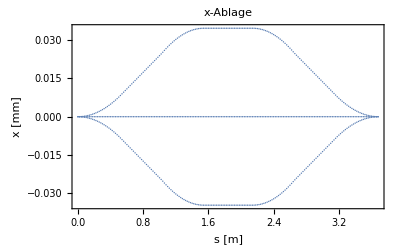

```mathematica
PlotXablage[test2]
```

Wie ist das mit D' ?

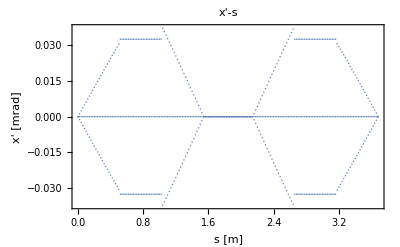

```mathematica
PlotXprime[test2]
```

Man kann sich auch die Bewegung im horizontalen Phasenraum ansehen, mit PlotXphase. Das macht aber die Phasenraumverteilung für viele Teilchen an einem Ort. Wir wollen jetzt hier wenig Teilchen an allen Orten "s" sehen. 
Die Struktur der Daten ist so : 1. Index position, 2. Index Teilchen, 3. Index die Koordinaten. 
Wenn wir also die Position aufgeben wollen, brauchen wir nur den ersten Index "platt" zu machenn, mit Flatten:

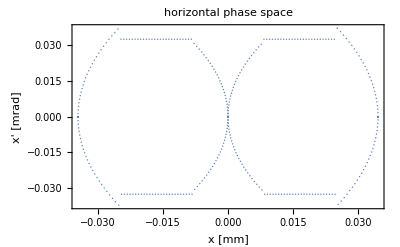

```mathematica
PlotXphase[Flatten[test2,1]]
```

Erkären Sie mal was man da sieht ...

Ebenso können Sie sich ansehen wie sich die s-Position der Teilchen "entwickelt"...

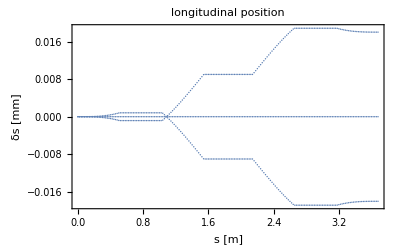

```mathematica
PlotSpos[test2]
```

Jetzt machen Sie doch mal einen ganzen bunch, sagen wir 1000 Teilchen. Wir kümmern und nicht um die transversalen Koordinaten aber wie generieren eine Impulsverteilung und eine Bunchlänge. Beide normaltverteilt, Mittelwert   = 0.  σ_p = 10^-4  (Das ist die relative Impulsabweichung vom Nominalimpuls), σ_s=1 mm. ‚
Bekommen Sie das hin ? Normalverteilte Zufallszahlen macht man mit RandomReal[NormalDistribution[..., es müssen aber immer alle 6 Koordinaten sein, die anderen Fünf sind Nullen. 
Also entweder mit Table, oder wie immer sie wollen.

```mathematica
set1 = Table[{0,{0,0,0,0,RandomReal[NormalDistribution[0,0.001]],RandomReal[NormalDistribution[0,0.0001]]}},{1000}];
```

und den jagen wir dann mal durch die Dipole, erstmal wieder an allen Stützstellen.

```mathematica
test3 = track[compnum,#,set1] & /@ plist;
```

Jetzt schauen Sie sich mal die Entwicklung der s-Position an, oder den longitudinalen Phasenraum. 
Wir der bunch kürzer ??

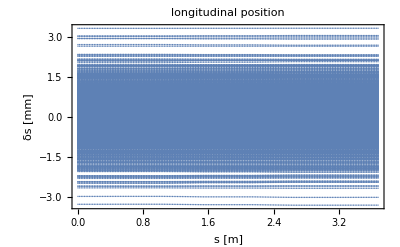

```mathematica
PlotSpos[test3]
```

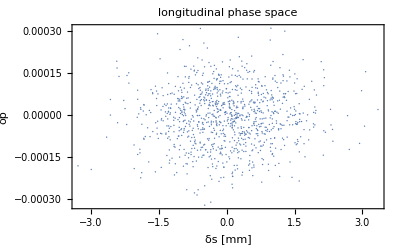

```mathematica
PlotSphase[Last[test3]]
```

Nein, wird er nicht. Zum Kompressor gehört auch eine HF - cavity die dem bunch einen, und zwar den richtigen, "chirp" verpasst, d.h. eine von δs abhängige Impulsabweichung.
Die HF im Resonator schwingt ja periodisch, d.h. jede endliche Bunchlänge führt zu einer s-abhängigen Impulsänderung da das Feld ja nicht zeitlich konstant ist. 
Bezeichnen wir mit ϕ_0 die Phase der HF für das Referenzteilchen, dann sieht ein Teilchen mit Abweichung "δs" das Feld zur Phase ϕ_0+k_HF*δ_s. 
Dabei ist k_HF = 2 π f_HF/c . Wir können hier getrost β = 1 annehmen, die Teilchen haben praktisch v=c und die relative Impulsänderung ist auch gleich der relativen Änderung der kinetischen Energie. 
Dann ist die relative Impulsänderung :

δp_cav= ΔE_cav*Cos[ ϕ_0+k_HF*δ_s]/(E_in+ΔE_cav*Cos[ϕ_0])

Das bekommen Sie sicher selbst programmiert. Die Parameter : f_HF= 1.3 GHz,  ΔE_cav= 120 MeV, E_in= 50 MeV. 

Sie schreiben am besten eine kleine Routine in die man einen Teilchen-Vektor reinsteckt und wieder einen rausbekommt. Mit ϕ0 als freiem Parameter. Achtung : unsere Listen sind immer {s, {x,x',y,y',δs,δp}}. Rauskommen muss also  {s, {x,x',y,y', δs, δp+δpcav}}

```mathematica
chirp[{s_,{x_,xs_,z_,zs_,δs_,δp_}},ϕ0_]:=Module[{δpcav1,δp1},
δpcav1= Δecav*Cos[ϕ0+(2*Pi*fhf)/c*δs]/(ein+Δecav*Cos[ϕ0]);
δp1=δp+δpcav1;
Return[{s,{x,xs,z,zs,δs,δp1}}]]
```

Diese Funktion können Sie dann über den Startsatz (set1) darüber mappen und anschliessend durch die Dipole laufen lassen. 
Ich würde das nur zum Endpunkt machen und mir dort den longitudinalen Phasenraum ansehen. 
Das geht so flott dass man es problemlos mit Manipulate machen und mit der Phase ϕ_0 spielen kann. 
Welche Phase würden sie dann reindrehen um den Bunch optimal zu verkürzen ? 

Statt den Phasenraum anzusehen können Sie auch "PlotShisto" verwenden, das zeigt die Teilchendichteverteilung.

```mathematica
(*δpcav[vecin_,ϕ0_]:=*)
```

```mathematica
(*test4man[ϕ0_] := track[compnum,ltot,δpcav[#,ϕ0]&/@ set1]*)
```

```mathematica
test4man[ϕ0_]:= track[compnum,ltot,chirp[#,ϕ0]&/@set1]//. {fhf-> 1.3*10^9,c-> 3.*10^8,Δecav-> 120.*10^6,ein -> 50.*10^6}
```

```mathematica
Manipulate[PlotSphase[test4man[ϕ0]],{ϕ0,0,2*Pi}]
```

Den kürzesten Bunch hat man für ϕ0 = π/2

So, das war jetzt aber eine Weihnachtsgeschenk-Aufgabe deren Erstellung mich hoffentlich deutlich mehr Stunden gekostet hat als Sie die Bearbeitung :-)

#### Anmerkung :

Seit einigen Jahren verwenden wir bei FLASH einen zweiten zusäzlichen HF Resonator der mit 3*f_HF= 3.9 GHz betrieben wird. 
Könnten Sie ahnen wozu ? 
Man oder Frau kann das natürlich als Ansporn begreifen das noch einzubauen. Dann haben Sie zwei weitere Parameter zum Spielen, die Phase ϕ_39 und die Amplitude E_39 dieser Cavity. Damit kann man dann im Phasenraum interessante Dinge treiben.